```mathematica
f[x_]:=ⅇ^((-x^2)/2)
y:=Table[ⅇ^((-x^2)/2),{x,-10,10,1}]
y
A:={{-10,1/ⅇ^50},{-9,1/ⅇ^(81/2)},{-8,1/ⅇ^32},{-7,1/ⅇ^(49/2)},{-6,1/ⅇ^18},{-5,1/ⅇ^(25/2)},{-4,1/ⅇ^8},{-3,1/ⅇ^(9/2)},{-2,1/ⅇ^2},{-1,1/(√ⅇ)}}
B:={{1,1/(√ⅇ)},{2,1/ⅇ^2},{3,1/ⅇ^(9/2)},{4,1/ⅇ^8},{5,1/ⅇ^(25/2)},{6,1/ⅇ^18},{7,1/ⅇ^(49/2)},{8,1/ⅇ^32},{9,1/ⅇ^(81/2)},{10,1/ⅇ^50}}
G1=ListPlot[A,PlotStyle->{RGBColor[1,0,0],PointSize[0.03]}]
G2=ListPlot[B,PlotStyle->{RGBColor[0,0,1],PointSize[0.02]}]
Show[G1,G2]
S1:=Interpolation[A]
S2:=Interpolation[B]
U=Plot[S1[x],{x,-10,-1}]
V=Plot[S2[x],{x,1,10}]
Show[U,V]

Clear[S1]
n:=8;
h:=10/n;
f[z_]:=1/(z^2+2)
H:=Table[{x,f[x]},{x,-6,6 ,h}]
S1:=Interpolation[H]
Plot[{f[z],S1[z]},{z,-6,6},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]}]
δ:=Table[N[Abs[S1[x]-f[x]]],{x,-6,6,1}]
Print["Pentru n=",n,"eroarea este",Max[δ]]
```

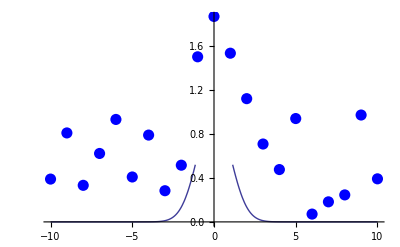

```mathematica
g[x_]:=ⅇ^((-x^2)/2)+Random[]
A:=Table[N[{x,g[x]}],{x,-10,10}]
B:=Table[v,{v,-10,10}]

H:=Fit[A,{1,x,x^2},x]

M:=H/.x->B
G1:=ListPlot[A,PlotStyle->{RGBColor[0,0,1],PointSize[0.02]}]
G2:=Plot[ⅇ^((-x^2)/2),{x,-10,10}]
Show[G1,G2]
```